## unclean code

```mathematica
ClearAll[η];
FullSimplify[RegionMember[StadiumShape[{{0,0},{η,0}},1],{x,y}],Assumptions->{(x|y)∈Reals,η>0}]
```

x^2+y^2≤1||y^2+(x-η)^2≤1||(η≥x&&x≥0&&-η≤-y η≤η)

```mathematica
ClearAll[η];
reg=ImplicitRegion[x<=0&&x^2+y^2==1||x>=η&&y^2+(x-η)^2==1||η≥x&&x≥0&&(y==1)||η≥x&&x≥0&&(y==-1),{x,y}];
```

```mathematica
(*reg=Circle[{0,0},{4,2}];
RegionPlot[reg,Method->{"DiscretizationMethod"->"Symbolic"},AspectRatio->Automatic]*)
```

```mathematica
ClearAll[arc,η];
arc[{x_,y_}]:=Which[
x>η,If[y>0,PlanarAngle[{η,0}->{{η+1,0},{x,y}}],3π/2+2η+PlanarAngle[{η,0}->{{η,-1},{x,y}}]],
0<=x<=η,If[y>0,π/2+x,3π/2+η+x],
True,π/2+η+PlanarAngle[{0,0}->{{0,1},{x,y}}]
]
```

```mathematica
η=RandomReal[];
α=RandomReal[{0,-π/2}];
{px,py}={Cos[α]+η,Sin[α]};
Graphics[{{Opacity[.2],EdgeForm[Black],FaceForm[],StadiumShape[{{0,0},{η,0}},1]},{Red,PointSize[Large],Point[{η+1,0}],Green,Point[{px,py}]}},PlotLabel->{η,arc[{px,py}]==2π+2η+α}]
```

-Graphics-

```mathematica
η=RandomReal[];
α=RandomReal[{π/2,3π/2}];
{px,py}={Cos[α],Sin[α]};
Graphics[{{Opacity[.2],EdgeForm[Black],FaceForm[],StadiumShape[{{0,0},{η,0}},1]},{Red,PointSize[Large],Point[{η+1,0}],Green,Point[{px,py}]}},PlotLabel->{η,arc[{px,py}]==α+η}]
```

-Graphics-

```mathematica
η=RandomReal[];
{px,py}={RandomReal[{0,η}],-1};
Graphics[{{Opacity[.2],EdgeForm[Black],FaceForm[],StadiumShape[{{0,0},{η,0}},1]},{Red,PointSize[Large],Point[{η+1,0}],Green,Point[{px,py}]}},PlotLabel->{η,arc[{px,py}]==px+3π/2+η}]
```

-Graphics-

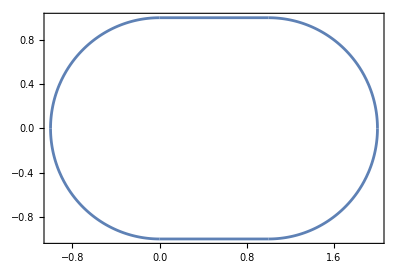

```mathematica
η=1;
regP=RegionPlot[reg,Method->{"DiscretizationMethod"->"Symbolic"},AspectRatio->Automatic]
```

```mathematica
Solve[{y1==a0 x1+b0,y2==a0 x2+b0},{a0,b0}]
```

```mathematica
ClearAll[η];
slope=ImplicitD[y^2+(x-η)^2==1,y,x]
FullSimplify[{Cos[ArcTan[slope]],Sin[ArcTan[slope]]},Assumptions->{y^2+(x-η)^2==1,y∈Reals}]
```

(-x+η)/y

{Abs[y],(-x+η)/Sign[y]}

```mathematica
ClearAll[tangent];
tangent[{px_,py_}]:=Which[
px<0,{Abs[py],-px/(Sign@py)},
px>η,{Abs[py],(-px+η)/(Sign@py)},
True,{1,0}]
```

```mathematica
ClearAll[crossing,next];
crossing[{x1_,y1_},{x2_,y2_}]:=Module[{a0=-(-y1+y2)/(x1-x2),b0=-(x2 y1-x1 y2)/(x1-x2)},{{x1,y1},SortBy[Quiet@SolveValues[{y==a0 x+b0},{x,y}∈reg],Norm[{x1,y1}-#]&][[-1]]}];
next[{p1_,p2_}]:=crossing[p2,ReflectionTransform[tangent[p2],p2][p1]]
```

```mathematica
ClearAll[plotReflection];
plotReflection[{p1_,p2_}]:=Graphics[{{Opacity[.2],EdgeForm[Black],FaceForm[],StadiumShape[{{0,0},{η,0}},1]},{Green,Arrow[{p1,p2}],Arrow[next[{p1,p2}]]},{Blue,InfiniteLine[p2,tangent[p2]]},{Red,PointSize[Large],Point[p1],Point[next[{p1,p2}]]}}]
```

```mathematica
η=1;
p1={η+1,0};
p2=RandomPoint[reg];
```

```mathematica
plotReflection/@NestList[next,{p1,p2},5]//Show
```

-Graphics-

```mathematica
η=1;
α0=ArcCos[1/ⅇ];
p1=N@{η+Cos[1],Sin[1]};
p2=SortBy[crossing[p1,p1-{Sin[α0],Cos[α0]}],Norm[#-p1]&][[2]](*RandomPoint[reg]*);
```

```mathematica
α0/π 180.
```

68.4151

```mathematica
Show[Graphics[{{Opacity[.2],EdgeForm[Black],FaceForm[],StadiumShape[{{0,0},{η,0}},1]},{Red,PointSize[Large],Point[{p1,p2}]},{Blue,InfiniteLine[p1,tangent[p1]],Line[{p1,p2}]}}],ListPlot[{p1,p2}->Range[2]]]
```

-Graphics-

```mathematica
bounces=5000;
data=NestList[next,{p1,p2},bounces];
collision=Partition[DeleteDuplicates@Flatten[data,1],3,1];
θ=1/2(Module[{q1,p,q2},
{q1,p,q2}=#;Sign[Cross[Append[0][p-q1],Append[0][q2-p]][[-1]]]]PlanarAngle[#])&/@collision;
```

```mathematica
bn=6;
Show[Graphics[{{Opacity[.2],EdgeForm[Black],FaceForm[],StadiumShape[{{0,0},{η,0}},1]},{Red,Line/@data[[;;bn]]}}],With[{pnts=DeleteDuplicates@Flatten[data,1][[;;2bn]]},ListPlot[pnts->Range[Length[pnts]]]],PlotRange->{{-2,η+2},{-2,2}}]
```

-Graphics-

```mathematica
Graphics[{{Opacity[.2],EdgeForm[Black],FaceForm[],StadiumShape[{{0,0},{η,0}},1]},{Red,Line/@data}}]
```

-Graphics-

```mathematica
s=arc/@collision[[All,2]];
```

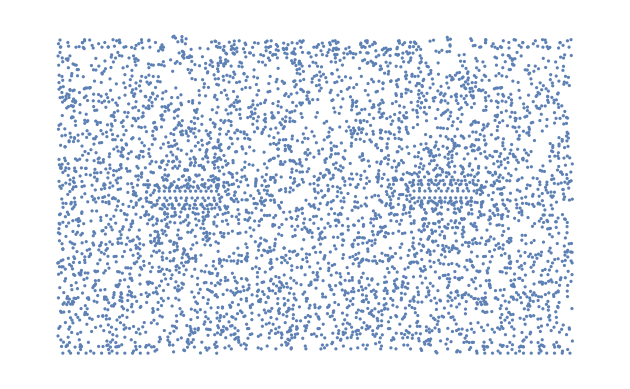

```mathematica
ListPlot[Transpose[{s/(2π+2η),Sin[θ]}],PlotRange->{{0,1},{-1,1}},Axes->False]
```

## Clean code

https://michaelberryphysics.wordpress.com/wp-content/uploads/2013/07/berry102.pdf

```mathematica
ClearAll[η,reg];
reg=ImplicitRegion[x<=0&&x^2+y^2==1||x>=η&&y^2+(x-η)^2==1||η≥x&&x≥0&&(y==1)||η≥x&&x≥0&&(y==-1),{x,y}];
```

```mathematica
ClearAll[arc,η];
arc[{x_,y_}]:=Which[
x>η,If[y>0,PlanarAngle[{η,0}->{{η+1,0},{x,y}}],3π/2+2η+PlanarAngle[{η,0}->{{η,-1},{x,y}}]],
0<=x<=η,If[y>0,π/2+x,3π/2+η+x],
True,π/2+η+PlanarAngle[{0,0}->{{0,1},{x,y}}]
]
```

```mathematica
ClearAll[tangent];
tangent[{px_,py_}]:=Which[
px<0,{Abs[py],-px/(Sign@py)},
px>η,{Abs[py],(-px+η)/(Sign@py)},
True,{1,0}]
```

```mathematica
ClearAll[crossing,next];
crossing[{x1_,y1_},{x2_,y2_}]:=Module[{a0=-(-y1+y2)/(x1-x2),b0=-(x2 y1-x1 y2)/(x1-x2)},{{x1,y1},SortBy[Quiet@SolveValues[{y==a0 x+b0},{x,y}∈reg],Norm[{x1,y1}-#]&][[-1]]}];
next[{p1_,p2_}]:=crossing[p2,ReflectionTransform[tangent[p2],p2][p1]]
```

```mathematica
η=.01;
α0=ArcCos[1/ⅇ];
p1=N@{η+Cos[1],Sin[1]};
p2=SortBy[crossing[p1,p1-{Sin[α0],Cos[α0]}],Norm[#-p1]&][[2]](*RandomPoint[reg]*);
```

```mathematica
α0/π 180.
```

68.4151

```mathematica
Show[Graphics[{{Opacity[.2],EdgeForm[Black],FaceForm[],StadiumShape[{{0,0},{η,0}},1]},{Red,PointSize[Large],Point[{p1,p2}]},{Blue,InfiniteLine[p1,tangent[p1]],Line[{p1,p2}]}}],ListPlot[{p1,p2}->Range[2]]]
```

-Graphics-

```mathematica
bounces=10000;
data=NestList[next,{p1,p2},bounces];
collision=Partition[DeleteDuplicates@Flatten[data,1],3,1];
```

```mathematica
collision//Length
```

10000

```mathematica
θ=1/2(Module[{q1,p,q2},
{q1,p,q2}=#;Sign[Cross[Append[0][p-q1],Append[0][q2-p]][[-1]]]]PlanarAngle[#])&/@collision;
```

```mathematica
Manipulate[
Show[With[{pnts=DeleteDuplicates@Flatten[data,1][[;;2bn]]},ListPlot[pnts->Range[Length[pnts]],Axes->False]],Graphics[{{Opacity[.2],EdgeForm[Black],FaceForm[],StadiumShape[{{0,0},{η,0}},1]},{Red,Line/@data[[;;bn]]}}],PlotRange->All],{bn,1,100,1}]
```

```mathematica
Graphics[{{Opacity[.2],EdgeForm[Black],FaceForm[],StadiumShape[{{0,0},{η,0}},1]},{Red,Line/@data}}]
```

-Graphics-

```mathematica
s=arc/@collision[[All,2]];
```

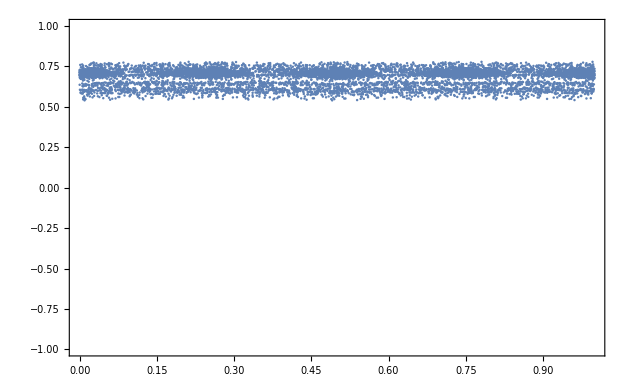

```mathematica
ListPlot[Transpose[{s/(2π+2η),Sin[θ]}],PlotRange->{{0,1},{-1,1}},Axes->False,Frame->True]
```

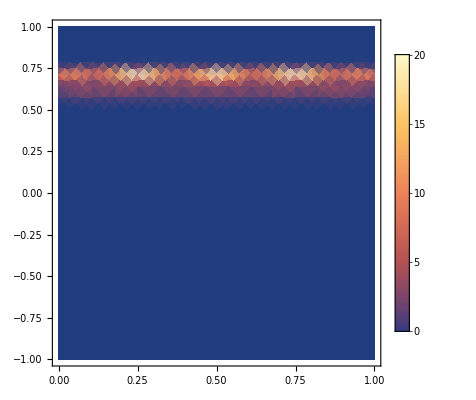

```mathematica
SmoothDensityHistogram[Transpose[{s/(2π+2η),Sin[θ]}],Automatic,"PDF",PlotLegends->Automatic,PlotRange->{{0,1},{-1,1}}]
```

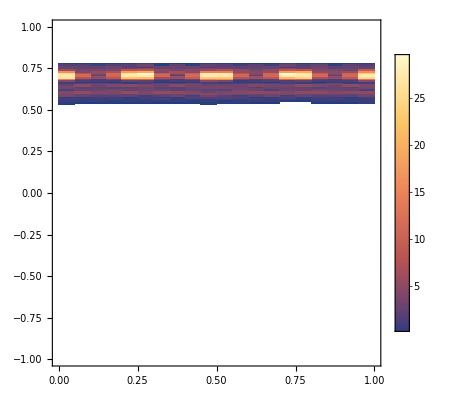

```mathematica
DensityHistogram[Transpose[{s/(2π+2η),Sin[θ]}],Automatic,"PDF",ChartLegends->Automatic,PlotRange->{{0,1},{-1,1}}]
```

## eclipse: unclean

```mathematica
ClearAll[a,b]
ImplicitD[x^2/a^2+y^2/b^2==1,y,x]
```

-(b^2 x)/(a^2 y)

```mathematica
a=1;b=.5;
c=√(a^2-b^2);
reg=Circle[{0,0},{a,b}];
```

```mathematica
ClearAll[tangent,crossing,next];
tangent[{px_,py_}]:=Reverse@{b^2 px,-a^2 py}
crossing[{x1_,y1_},{x2_,y2_}]:=Module[{a0=-(-y1+y2)/(x1-x2),b0=-(x2 y1-x1 y2)/(x1-x2)},{{x1,y1},SortBy[Quiet@SolveValues[{y==a0 x+b0,x^2/a^2+y^2/b^2==1},{x,y},Reals,WorkingPrecision->MachinePrecision],Norm[{x1,y1}-#]&][[-1]]}];
next[{p1_,p2_}]:=crossing[p2,ReflectionTransform[tangent[p2],p2][p1]]
```

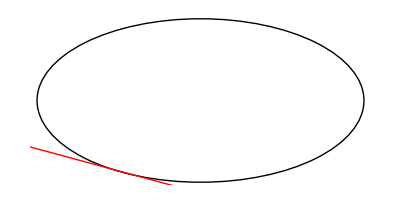

```mathematica
p=RandomPoint[reg];
Graphics[{{reg},{Red,InfiniteLine[p,tangent[p]]}}]
```

```mathematica
{p1,p2}=data2[[;;2]](*RandomPoint[reg,2]*);
```

```mathematica
bounces=100;
data=NestList[next,{p1,p2},bounces];
collision=Partition[DeleteDuplicates@Flatten[data,1],3,1];
```

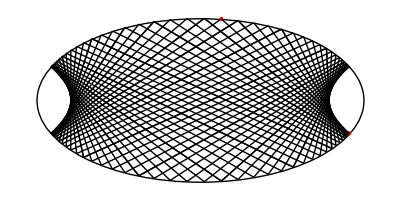

```mathematica
Graphics[{{reg},{Red,PointSize[Large],Point[{p1,p2}]},{Line/@data}}]
```

```mathematica
sol=FindInstance[ArcLength@Circle[{0,0},{a,b},{0,a}]==1,a][[1]]
```

{a→1.35855}

```mathematica
p1={a Cos[a],b Sin[a]}/.sol
```

{0.210656,0.48878}

```mathematica
Show[ParametricPlot[{a Cos[t],b Sin[t]},{t,0,θ=1.3},PlotStyle->Red],ParametricPlot[{a Cos[t],b Sin[t]},{t,θ,2π}],PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
Graphics[{{reg},{Red,PointSize[Large],Point[p1],Green,Point[{a,0}],Blue,Point[{0,0}]},{Red,Thick,Circle[{0,0},{a,b},{0,a}]/.sol}}]
```

```mathematica
RandomPoint[InfiniteLine[p2,{-a^2 p2[[2]],b^2p2[[1]]}],2]
```

RandomPoint::unbndreg: The specified region appears to be unbounded. Appropriate bounds will be automatically computed. Explicit bounds may be specified as a third argument.

{{0.0689973,-0.514276},{-0.136038,-0.495797}}

```mathematica
α=ArcCos[1/ⅇ];
p2=SortBy[RegionIntersection[reg,HalfLine[p1,-{Cos[α],Sin[α]}]][[1]],Norm[#-p1]&][[-1]];
Graphics[{{reg},{Red,PointSize[Large],Point[p1],Green,Point[{a,0}],Blue,Point[{0,0}]},{Red,Thick,Circle[{0,0},{a,b},{0,a}]/.sol},{Line[{p1,p2}]},{Blue,Point[RandomPoint[InfiniteLine[p2,{-a^2 p2[[2]],b^2p2[[1]]}],2]],InfiniteLine[p2,{-a^2 p2[[2]],b^2p2[[1]]}]},{Green,HalfLine[p2,-ReflectionTransform[{b^2 p2[[1]],-a^2 p2[[2]]},p2][p1]]}}]
```

RandomPoint::unbndreg: The specified region appears to be unbounded. Appropriate bounds will be automatically computed. Explicit bounds may be specified as a third argument.

-Graphics-

```mathematica
MatchQ[{{0.2106564996039441,0.48878007303249726},{-0.17739055925092453,-0.4920702667019833}},{_List,_List}]
```

True

```mathematica
ClearAll[nextBouncePoint,reflectHalfLine]
reflectHalfLine[{p1_,p2_}]:=HalfLine[p2,-ReflectionTransform[{b^2 p2[[1]],-a^2 p2[[2]]},p2][p1]]
nextBouncePoint[{p1_,p2_}]:=With[{pnts=RegionIntersection[reg,reflectHalfLine[{p1,p2}]][[1]]},If[MatchQ[pnts,{_List,_List}],SortBy[pnts,Norm[#-p2]&][[-1]],pnts]]
```

```mathematica
Line/@NestList[{#[[2]],nextBouncePoint[#]}&,{p1,p2},3]
```

{{{0.210656,0.48878},{-0.177391,-0.49207}},{{-0.177391,-0.49207},{-0.435246,0.450156}},{{-0.435246,0.450156},{-0.598412,-0.400594}},{{-0.598412,-0.400594},{-0.666536,0.372736}}}

```mathematica
{p1,p2}={{-0.8701830360745195,0.24636430531234196},{-0.27420749237067515,-0.4808352761413689}};
```

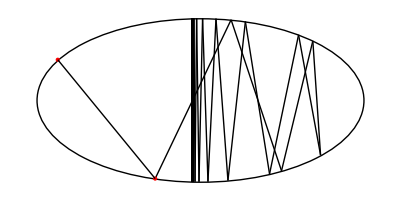

```mathematica
Graphics[{{reg},{Red,PointSize[Large],Point[{p1,p2}]},{Line/@NestList[{#[[2]],nextBouncePoint[#]}&,{p1,p2},100]}}]
```

### michael

```mathematica
nextReflectionPoint[{p_, dir_}, {a_,b_}] := 
Module[{solxy, distances,pos,x, y},
 solxy ={x, y}/.Quiet[Solve[{x == p[[1]] + s dir[[1]], 
         y== p[[2]] + s dir[[2]], 
x^2/a^2+y^2/b^2==1},{s,x,y}]];
distances = Norm[p-#]& /@ solxy;
pos=Position[distances,Max[distances]][[1]];
solxy[[#]]&@@pos
];
```

```mathematica
reflection[{p_, dir_},{a_, b_}] := 
Module[{normalDir,parallelDir,normalComponent,paralleComponent},
normalDir = -#/Norm[#]&[p/{a^2,b^2}];
parallelDir= Reverse[normalDir]{-1,1};
      normalComponent=normalDir.dir;
paralleComponent=parallelDir.dir;
{p,-normalComponent normalDir + paralleComponent parallelDir}
];
```

```mathematica
propagate[{p_, dir_},{a_, b_}] := 
Module[{p1},
p1=nextReflectionPoint[{p, dir}, {a,b}] ;
reflection[{p1, dir},{a, b}] 
];
```

```mathematica
makeStartData[φ_, α_,{a_,b_}] := 
Module[{p,normalDir,parallelDir},
p={a Cos[φ],b Sin[φ]};
normalDir = -#/Norm[#]&[p/{a^2,b^2}];
parallelDir= Reverse[normalDir]{-1,1};
{p, Cos[α] normalDir + Sin[α] parallelDir}
];
```

```mathematica
multiReflections[φ_, α_,n_, {a_,b_}] := 
NestList[propagate[#,{a, b}] &, makeStartData[φ, α,{a,b}] ,Round[n]];
```

```mathematica
ellipseMultiReflectionGraphics[φ_, α_,n_, {a_,b_}] := 
Module[{parameters,pathData,pathPoints},
parameters=N[Rationalize[{φ, α,n, {a,b}}, 0], 20 + 4 n];
pathData = multiReflections@@ parameters;
pathPoints = N[First /@ pathData];
Graphics[{{GrayLevel[0.95],Disk[{0,0},{a,b}]},
{Black,PointSize[0.016], N@If[a >=b,Point[{{Sqrt[a^2-b^2], 0}, {-Sqrt[a^2-b^2], 0}}],
Point[{{0, Sqrt[b^2-a^2] }, {0, -Sqrt[b^2-a^2] }}]]},
{Black,Thickness[0.006],Point[pathPoints[[1]]]},
{Black,PointSize[0.02],Circle[{0,0},{a,b}]},
{Thickness[0.005], MapIndexed[{Hue[0.3 #2[[1]]/n+.6],Line[#1]}&,
Partition[pathPoints,2,1]]}},PlotRange->All,ImageSize->{500,400}]
];
```

```mathematica
Manipulate[
ellipseMultiReflectionGraphics[φ, α,n, {1,b}] ,
{{b, 1,"vertical half-axis length"}, 0.33, 3},
{{n, 10,"number of reflections"}, 1, 50, 1},
{{φ, 1,"starting position"},-Pi,Pi},
{{α,0,"starting angle"},-Pi/2+.01, Pi/2-.01},
SaveDefinitions->True,TrackedSymbols:>{b,n,φ,α}]
```

```mathematica
data2=multiReflections[-0.420973, 0,100, {1,.5}][[All,1]];
```

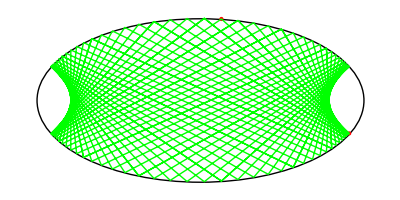

```mathematica
Graphics[{reg,Red,PointSize[Large],Point[data2[[;;2]]],Green,Line@data2}]
```

```mathematica
lines=Partition[data,2,1];
```

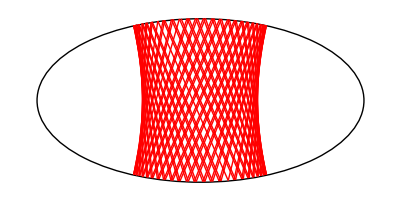

```mathematica
Graphics[{Circle[{0,0},{1,.5}],Red,Line/@lines,Green(*,Line[{p1,p2}]*)}]
```

```mathematica
angles=With[{θ=ArcTan[b/a(#[[1]])/(#[[2]])]},If[θ>0,θ,2π+θ]]&/@data[[2;;-2]]
```

{5.97725,0.396932,6.21724,5.94551,0.378515,6.26765,5.91862,0.354765,0.0351062,5.8969,0.325956,0.0852066,5.88061,0.292436,0.133991,5.86991,0.25463,0.180721,5.86493,0.21304,0.224707,5.86572,0.168242,0.265321,5.87226,0.120882,0.302007,5.88449,0.0716637,0.334283,5.90229,0.0213377,0.361746,5.92544,6.25387,0.384068,5.95368,6.20366,0.400994,5.98668,6.15469,0.412337,6.02402,6.10769,0.417975,6.06521,6.06336,0.417851,6.10967,6.02233,0.411963,6.15677,5.98516,0.400376,6.20581,5.95236,0.383213,6.25605,5.92433,0.360663,0.0235263,5.9014,0.332984,0.0738203,5.88385,0.300508,0.122973,5.87186,0.263643,0.170237,5.86556,0.222871,0.214909,5.86503,0.178753,0.256347,5.87026,0.131919,0.293977,5.8812,0.0830621,0.327302,5.89773,0.032922,0.355899,5.91967,6.26546,0.379424,5.94678,6.21508,0.397604,5.97873,6.16576,0.410239,6.01511,6.11824,0.417192,6.05546,6.07324}

```mathematica
s=ArcLength[Circle[{0,0},{a,b},{0,#}]]&/@angles
```

{4.68449,0.212723,4.81118,4.6664,0.201716,4.83645,4.65075,0.187738,0.0175639,4.63788,0.171098,0.0427572,4.6281,0.152152,0.0675902,4.62161,0.13128,0.091806,4.61857,0.108869,0.115102,4.61905,0.0852901,0.137131,4.62304,0.0608782,0.157517,4.63044,0.0359236,0.175873,4.64109,0.0106713,0.191822,4.65474,4.82956,0.205019,4.6711,4.80434,0.215171,4.6898,4.77945,0.222046,4.71047,4.75515,0.225485,4.73272,4.73173,0.225409,4.75619,4.70954,0.221819,4.78052,4.68895,0.214799,4.80542,4.67034,0.20451,4.83065,4.6541,0.191187,0.0117664,4.64057,0.175126,0.0370104,4.63005,0.156675,0.0619469,4.62279,0.13621,0.0863291,4.61896,0.114118,0.109865,4.61863,0.0907756,0.132217,4.62182,0.0665272,0.153013,4.62845,0.0416737,0.171868,4.63838,0.0164699,0.1884,4.65137,4.83536,0.202256,4.66713,4.81009,0.213128,4.68533,4.78511,0.22077,4.70558,4.76065,0.225006,4.72751,4.737}

```mathematica
θ=1/2(Module[{q1,p,q2},
{q1,p,q2}=#;Sign[Cross[Append[0][p-q1],Append[0][q2-p]][[-1]]]]PlanarAngle[#])&/@Partition[data,3,1]
```

{0.247441,0.115791,-0.355398,0.214612,0.155466,-0.359522,0.178744,0.192946,-0.358531,0.14035,0.227697,-0.352441,0.0999748,0.259223,-0.341337,0.0581908,0.28707,-0.325378,0.0155877,0.31084,-0.304793,-0.0272347,0.330192,-0.279876,-0.0696739,0.344849,-0.250985,-0.111132,0.354601,-0.218535,-0.151024,0.359308,-0.18299,-0.188783,0.358904,-0.144858,-0.223872,0.353395,-0.104681,-0.255791,0.342858,-0.0630287,-0.284081,0.327445,-0.0204891,-0.308336,0.307376,0.0223388,-0.32821,0.282938,0.0648523,-0.343416,0.254482,0.106453,-0.353738,0.222417,0.146553,-0.359028,0.187202,0.184584,-0.35921,0.149339,0.220006,-0.354283,0.109368,0.252311,-0.344316,0.0678549,0.281038,-0.329451,0.0253867,0.305775,-0.309902,-0.0174387,0.326166,-0.285948,-0.0600188,0.341919,-0.257932,-0.101754,0.352809,-0.226258,-0.142055,0.35868,-0.191379,-0.180351,0.359449,-0.153792,-0.216098,0.355105,-0.114034,-0.248785,0.345709,-0.0726685,-0.277943,0.331395,-0.0302796,-0.303156,0.31237}

```mathematica
θ//Length
s//Length
```

99

99

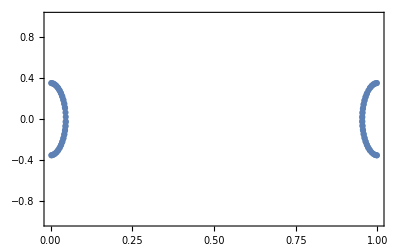

```mathematica
ListPlot[Transpose[{s/ArcLength[Circle[{0,0},{a,b},{0,2π}]],Sin[θ]}],PlotRange->{{0,1},{-1,1}},Axes->False,Frame->True]
```

## eclipse: clean

```mathematica
ClearAll[a,b]
ImplicitD[x^2/a^2+y^2/b^2==1,y,x]
```

-(b^2 x)/(a^2 y)

```mathematica
a=1;b=.5;
c=√(a^2-b^2);
reg=Circle[{0,0},{a,b}];
```

```mathematica
ClearAll[tangent,crossing,next];
tangent[{px_,py_}]:=Reverse@{b^2 px,-a^2 py}
crossing[{x1_,y1_},{x2_,y2_}]:=Module[{a0=-(-y1+y2)/(x1-x2),b0=-(x2 y1-x1 y2)/(x1-x2)},{{x1,y1},SortBy[Quiet@SolveValues[{y==a0 x+b0,x^2/a^2+y^2/b^2==1},{x,y},Reals,WorkingPrecision->MachinePrecision],Norm[{x1,y1}-#]&][[-1]]}];
next[{p1_,p2_}]:=crossing[p2,ReflectionTransform[tangent[p2],p2][p1]]
```

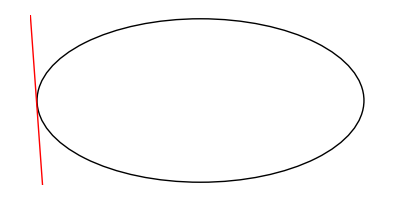

```mathematica
p=RandomPoint[reg];
Graphics[{{reg},{Red,InfiniteLine[p,tangent[p]]}}]
```

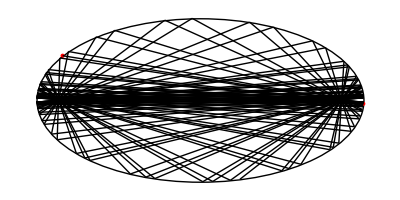

```mathematica
{p1,p2}=RandomPoint[reg,2];
bounces=100;
data=NestList[next,{p1,p2},bounces];
collision=Partition[DeleteDuplicates@Flatten[data,1],3,1];
Graphics[{{reg},{Red,PointSize[Large],Point[{p1,p2}]},{Line/@data}}]
```

```mathematica
θ=1/2(Module[{q1,p,q2},
{q1,p,q2}=#;Sign[Cross[Append[0][p-q1],Append[0][q2-p]][[-1]]]]PlanarAngle[#])&/@collision;
```

```mathematica
arcAngles=With[{θ=ArcTan[b/a(#[[1]])/(#[[2]])]},If[θ>0,θ,2π+θ]]&/@collision[[All,2]];
s=ArcLength[Circle[{0,0},{a,b},{0,#}]]&/@arcAngles;
```

```mathematica
θ//Length
s//Length
```

100

100

```mathematica
ℒ=ArcLength[Circle[{0,0},{a,b},{0,2π}]]
```

4.84422

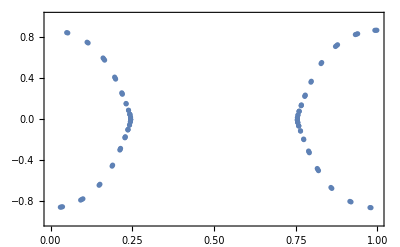

```mathematica
ListPlot[Transpose[{s/ℒ,Sin[θ]}],PlotRange->{{0,1},{-1,1}},Axes->False,Frame->True]
```